# Step-by-step setup of Kets, Operators, Commutators and Algebra for the Quantum Harmonic Oscillator in Mathematica

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx

## Introduction

This is a step-by-step tutorial on the use of Quantum Mathematica add-on to define kets, operators and commutators properties of the Harmonic Oscillator. This tutorial uses the notation of the book by C. Cohen-Tannoudji, B. Diu and F. Laloë, "Quantum Mechanics", Volume 1, Chapter V

## Load the Package

First load the Quantum`Notation` package. Write:
Needs["Quantum`Notation`"];
then press at the same time the keys ⇧-⌤ to evaluate. Mathematica will load the package:

```mathematica
Needs["Quantum`Notation`"]
```

Quantum`Notation` Version 2.2.0. (July 2010) 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

In order to use the keyboard to enter quantum objects write:
SetQuantumAliases[ ];
then press at the same time the keys ⇧-⌤ to evaluate. The semicolon prevents Mathematica from printing the help message. Remember that SetQuantumAliases[ ] must be evaluated again in each new notebook:

```mathematica
SetQuantumAliases[];
```

## Step-by-step implementation of the harmonic oscillator

In order to enter a ket similar to those that appear in the book of Cohen-Tannoudji, Chapter V, press the keyboard keys (this will only work in a Mathematica document where SetQuantumAliases[] has been executed): 
[ESC]ket[ESC]
The ket template will appear. Next press the keys:
[TAB][ESC]su[ESC]
A subscript template will appear inside the ket. Next press the keys:
[TAB][ESC]phi[ESC][TAB]n
Finally press at the same time the keys ⇧-⌤ to evaluate:

```mathematica
|Subscript[ϕ, n]⟩
```

|ϕ_n⟩

Here we define the effect of the operator "a" on the ket |ϕ_n⟩. The standard Mathematica symbol :> can be entered pressing the keys [ESC]:>[ESC], and the square root symbol can be entered by pressing at the same time the keys [CTRL]2. Notice the use of the underscore _ on the left hand side of the assignment, in the subscript |ϕ_n_⟩:

```mathematica
DefineOperatorOnKets[a,{|Subscript[ϕ, n_]⟩:>√n|Subscript[ϕ, n-1]⟩}]
```

|ϕ_n_⟩:>√n |ϕ_(n-1)⟩

In order to enter the operator in the appropiate syntax press the keys: 
a[ESC]on[ESC]
after that enter |ϕ_n⟩ as it was done above.
Finally press at the same time the keys [SHIFT] and [ENTER] to evaluate:

```mathematica
a·|Subscript[ϕ, n]⟩
```

√n |ϕ_(-1+n)⟩

Powers of the operator on the ket are also calculated (in order to write the power superscript, you can either use the standard Mathematica shortcut, pressing at the same time the keys [CTRL]6 or you can use the Quantum shortcut [ESC]po[ESC]):

```mathematica
a^3·|Subscript[ϕ, n]⟩
```

√(-2+n) √(-1+n) √n |ϕ_(-3+n)⟩

The definition works for numerical states (copy-paste the previous input from your Mathematica document and change "n" to 7):

```mathematica
a·|Subscript[ϕ, 7]⟩
```

√7 |ϕ_6⟩

The definition of an operator on a ket also defines the operation of a bra on the hermitian conjugate of the operator (press [ESC]bra[ESC] for the bra template,  [ESC]on[ESC] for the infix symbol "·" and [ESC]her[ESC] for the hermitian conjugate template):

```mathematica
⟨Subscript[ϕ, 7]|·SuperDagger[(a)]
```

√7 ⟨ϕ_6|

In order to enter a power of the hermitian conjugate of operator a, press the keys:
a[CTRL]6[ESC]dg [ESC][SPACE]3

```mathematica
⟨Subscript[ϕ, 7]|·a^(† 3)
```

√210 ⟨ϕ_4|

However the effect of the hermitian conjugate of the operator on a ket is undefined  (press [ESC]her[ESC] for the hermitian conjugate template, or press  a[CTRL]6[ESC]dg[ESC]):

```mathematica
SuperDagger[a]·|Subscript[ϕ, 7]⟩
```

a^†·|ϕ_7⟩

The effect of the hermitian conjugate of the operator on a ket can be defined using DefineOperatorOnKets. Notice the use of the underscore _ on the left hand side of the assignment, in the subscript

```mathematica
DefineOperatorOnKets[SuperDagger[a],{|Subscript[ϕ, n_]⟩:>√(n+1)|Subscript[ϕ, n+1]⟩}]
```

|ϕ_n_⟩:>√(n+1) |ϕ_(n+1)⟩

This time a^† acts on the ket:

```mathematica
SuperDagger[a]·|Subscript[ϕ, 7]⟩
```

2 √2 |ϕ_8⟩

In order to enter a power of the hermitian conjugate of operator a, press the keys:
aCtrl6[ESC]dg [ESC]␣3

```mathematica
a^(† 3)·|Subscript[ϕ, 7]⟩
```

12 √5 |ϕ_10⟩

We can try calculating matrix elements, however Mathematica does not know (yet) that these vectors are orthonormal:

```mathematica
⟨Subscript[ϕ, 8]|·SuperDagger[a]·|Subscript[ϕ, 7]⟩
```

2 √2 ⟨ϕ_8|ϕ_8⟩

Next we indicate that the kets are orthonormal. The standard Mathematica command KroneckerDelta is used. Notice that no output will be generated after pressing ⇧-⌤ in this command, because it is a delayed assignment (using := instead of =), and also notice the use of the underscores _ in the left-hand side of the assignment:

```mathematica
⟨Subscript[ϕ, j_]|·|Subscript[ϕ, k_]⟩:=KroneckerDelta[j-k]
```

Now the vectors are orthonormal:

```mathematica
⟨Subscript[ϕ, 8]|·|Subscript[ϕ, 8]⟩
```

1

```mathematica
⟨Subscript[ϕ, 8]|·|Subscript[ϕ, 9]⟩
```

0

```mathematica
⟨Subscript[ϕ, m]|·|Subscript[ϕ, n]⟩
```

KroneckerDelta[m-n]

Now we can get our matrix element:

```mathematica
⟨Subscript[ϕ, 8]|·SuperDagger[a]·|Subscript[ϕ, 7]⟩
```

2 √2

We can use the standard Mathematica command Table to generate a matrix representing the operator "a" for a finite number of states. This matrix corresponds to the matrix (C-24-a) in the page 499 in the book of Cohen-Tannoudji.

```mathematica
mymatrix=Table[⟨Subscript[ϕ, j]|·a·|Subscript[ϕ, k]⟩,{j,1,8},{k,1,8}];
MatrixForm[mymatrix]
```

(0 | √2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | √6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √7 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 √2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Mathematica can calculate the effect of "algebraic" expressions including the operators and kets that were defined above (in order to write the power superscript, you can either use the standard Mathematica shortcut, pressing at the same time the keys Ctrl6 or you can use the Quantum shortcut [ESC]po[ESC]):

```mathematica
(a+SuperDagger[a])^2·|Subscript[ϕ, 7]⟩
```

√42 |ϕ_5⟩+15 |ϕ_7⟩+6 √2 |ϕ_9⟩

Here is a TEX version of the result:

```mathematica
TeXForm[√42 |Subscript[ϕ, 5]⟩+15 |Subscript[ϕ, 7]⟩+6 √2 |Subscript[ϕ, 9]⟩]
```

\sqrt{42} \left|\phi _5\right\rangle +15 \left|\phi
   _7\right\rangle +6 \sqrt{2} \left|\phi
   _9\right\rangle

On the other hand, the expression itself does not evolve to any result:

```mathematica
(a+SuperDagger[a])^2
```

(a+a^†)^2

We can expand the expression using the command Expand:

```mathematica
Expand[(a+SuperDagger[a])^2]
```

a^2+a^†·a+a·a^†+(a^†)^2

The expansion has exactly the same effect on a ket as the original expresion:

```mathematica
(a^2+SuperDagger[a]·a+a·SuperDagger[a]+(SuperDagger[a])^2)·|Subscript[ϕ, 7]⟩
```

√42 |ϕ_5⟩+15 |ϕ_7⟩+6 √2 |ϕ_9⟩

Another type of expansion (using commutators) is obtained with the Quantum Mathematica command CommutatorExpand. However, Mathematica does not know (yet) that the commutator of these operators is equal to one.

```mathematica
CommutatorExpand[(a+SuperDagger[a])^2]
```

a^2-⟦a,a^†⟧_-+2 a·a^†+(a^†)^2

A different expansion is obtained with the option ReverseOrdering → True (the standard Mathematica symbol -> can be entered pressing the keys [ESC]->[ESC]):

```mathematica
CommutatorExpand[(a+SuperDagger[a])^2,ReverseOrdering->True]
```

a^2-⟦a^†,a⟧_-+2 a^†·a+(a^†)^2

The expansion has exactly the same effect on a ket as the original expresion:

```mathematica
(a^2-⟦SuperDagger[a],a⟧_-+2 SuperDagger[a]·a+(SuperDagger[a])^2)·|Subscript[ϕ, 7]⟩
```

√42 |ϕ_5⟩+15 |ϕ_7⟩+6 √2 |ϕ_9⟩

The Quantum Mathematica command EvaluateCommutators forces the evaluation of commutators. Notice that the result is the same as before:

```mathematica
EvaluateCommutators[(a^2-⟦SuperDagger[a],a⟧_-+2 SuperDagger[a]·a+(SuperDagger[a])^2)]
```

a^2+a^†·a+a·a^†+(a^†)^2

The TraditionalForm of an expression is usually easier to read:

```mathematica
TraditionalForm[a^2+SuperDagger[a]·a+a·SuperDagger[a]+(SuperDagger[a])^2]
```

a^†a+a a^†+(a^†)^2+a^2

Here the value "one" is assigned to the commutator. Press the keys [ESC]comm[ESC] in order to enter the commutator template:

```mathematica
⟦a,SuperDagger[a]⟧_-=1
```

1

This time QuantumExpand uses the value of the commutator:

```mathematica
CommutatorExpand[(a+SuperDagger[a])^2]
```

-1+a^2+2 a·a^†+(a^†)^2

The TraditionalForm representation can be easier to read:

```mathematica
TraditionalForm[CommutatorExpand[(a+SuperDagger[a])^2]]
```

2 a a^†+(a^†)^2+a^2-1

Here is a TEX version of the TraditionalForm:

```mathematica
TeXForm[TraditionalForm[CommutatorExpand[(a+SuperDagger[a])^2]]]
```

2 aa^{\dagger }+\left(a^{\dagger }\right)^2+a^2-1

Symbolic calculations can be performed:

```mathematica
(a+SuperDagger[a])^2·|Subscript[ϕ, k]⟩
```

√(-1+k) √k |ϕ_(-2+k)⟩+k |ϕ_k⟩+(1+k) |ϕ_k⟩+√(1+k) √(2+k) |ϕ_(2+k)⟩

Standard Mathematica commands (for example Collect) can be used on the expression:

```mathematica
Collect[(a+SuperDagger[a])^2·|Subscript[ϕ, k]⟩,|Subscript[ϕ, k]⟩]
```

√(-1+k) √k |ϕ_(-2+k)⟩+(1+2 k) |ϕ_k⟩+√(1+k) √(2+k) |ϕ_(2+k)⟩

Here is another simple example

```mathematica
(SuperDagger[a]·a)^3·|Subscript[ϕ, k]⟩
```

k^3 |ϕ_k⟩

This is the corresponding commutator expansion. It is using the known value for the commutator of these two operators:

```mathematica
CommutatorExpand[(SuperDagger[a]·a)^3]
```

-1+a·a^†-3 (-2 a+a^2·a^†)·a^†+(-3 a^2+a^3·a^†)·(a^†)^2

Expand and CommutatorExpand can be combined:

```mathematica
Expand[CommutatorExpand[(SuperDagger[a]·a)^3]]
```

-1+7 a·a^†-6 a^2·(a^†)^2+a^3·(a^†)^3

Quantum Mathematica commands as CollectFromRight can be used on this expression:

```mathematica
CollectFromRight[-1+7 a·SuperDagger[a]-6 a^2·(SuperDagger[a])^2+a^3·(SuperDagger[a])^3]
```

-1+(7 a+(-6 a^2+a^3·a^†)·a^†)·a^†

The result of the quantum expansion on a ket is the same as with the original expression:

```mathematica
Simplify[(-1+(7 a+(-6 a^2+a^3·SuperDagger[a])·SuperDagger[a])·SuperDagger[a])·|Subscript[ϕ, k]⟩]
```

k^3 |ϕ_k⟩

We define the position representation using the standard Mathematica command HermiteH and the standard Mathematica pattern _?NumberQ, which means that this definition will be used only when x is a number:

```mathematica
⟨x_?NumberQ|·|Subscript[ϕ, k_]⟩:=Exp[-x^2/2]*HermiteH[k,x]/√(2^k*k!*√Pi)
```

This is the value of the wave function when x=0.5

```mathematica
⟨0.5|·|Subscript[ϕ, 2]⟩
```

-0.234359

We can plot the wave function:

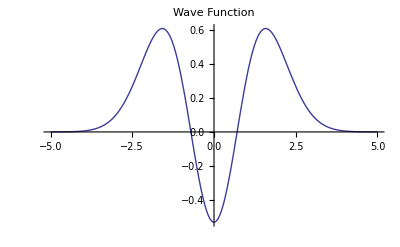

```mathematica
Plot[⟨x|·|Subscript[ϕ, 2]⟩,{x,-5,5},PlotLabel->"Wave Function"]
```

This is the value of the probability density function when x=0.5
(press the keys [ESC]norm[ESC] in order to write the quantum Norm template)

```mathematica
(‖⟨0.5|·|Subscript[ϕ, 2]⟩‖)^2
```

0.0549239

We can plot the probability density
(press the keys [ESC]norm[ESC] in order to write the quantum Norm template)

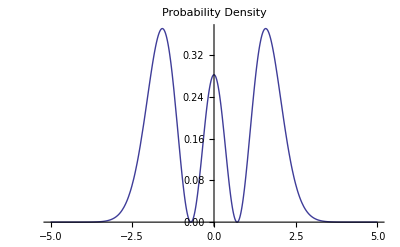

```mathematica
Plot[(‖⟨x|·|Subscript[ϕ, 2]⟩‖)^2,{x,-5,5},PlotLabel->"Probability Density"]
```

Next we verify that the function is normalized:

```mathematica
NIntegrate[(‖⟨x|·|Subscript[ϕ, 2]⟩‖)^2,{x,-5,5}]
```

1.

## Summary

These are all the definitions that were explained above. They correspond to the Quantum Harmonic Oscillator:

```mathematica
Needs["Quantum`Notation`"];
⟨Subscript[ϕ, j_]|·|Subscript[ϕ, k_]⟩:=KroneckerDelta[j-k];
DefineOperatorOnKets[a,{|Subscript[ϕ, n_]⟩:>√n|Subscript[ϕ, n-1]⟩}];
DefineOperatorOnKets[SuperDagger[(a)],{|Subscript[ϕ, n_]⟩:>√(n+1)|Subscript[ϕ, n+1]⟩}];
⟦a,SuperDagger[a]⟧_-=1;
⟨x_?NumberQ|·|Subscript[ϕ, k_]⟩:=Exp[-x^2/2]*HermiteH[k,x]/√(2^k*k!*√Pi);
```

Simple and complex operations can be performed after evaluating those definitions:

```mathematica
a^4·|Subscript[ϕ, 7]⟩
```

2 √210 |ϕ_3⟩

Simple and complex operations can be performed after evaluating those definitions:

```mathematica
CommutatorExpand[(a+SuperDagger[a])^3]
```

-3 a+a^3+3 a^2·a^†+3 a·(a^†)^2-3 a^†+(a^†)^3

Simple and complex operations can be performed after evaluating those definitions:

```mathematica
mymatrix=Table[⟨Subscript[ϕ, j]|·(a+SuperDagger[a])^3·|Subscript[ϕ, k]⟩,{j,1,8},{k,1,8}];
MatrixForm[mymatrix]
```

(0 | 6 √2 | 0 | 2 √6 | 0 | 0 | 0 | 0
6 √2 | 0 | 9 √3 | 0 | 2 √15 | 0 | 0 | 0
0 | 9 √3 | 0 | 24 | 0 | 2 √30 | 0 | 0
2 √6 | 0 | 24 | 0 | 15 √5 | 0 | √210 | 0
0 | 2 √15 | 0 | 15 √5 | 0 | 18 √6 | 0 | 4 √21
0 | 0 | 2 √30 | 0 | 18 √6 | 0 | 21 √7 | 0
0 | 0 | 0 | √210 | 0 | 21 √7 | 0 | 48 √2
0 | 0 | 0 | 0 | 4 √21 | 0 | 48 √2 | 0)

Simple and complex operations can be performed after evaluating those definitions:

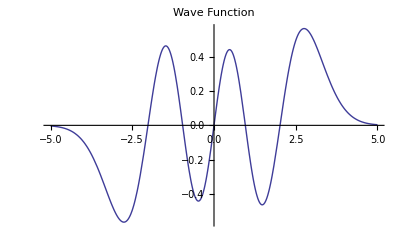

```mathematica
Plot[⟨x|·|Subscript[ϕ, 5]⟩,{x,-5,5},PlotLabel->"Wave Function"]
```

Simple and complex operations can be performed after evaluating those definitions:

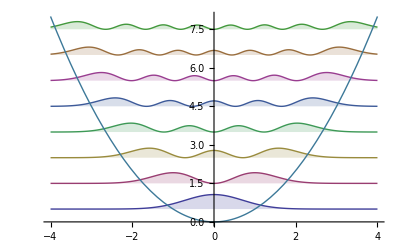

```mathematica
Plot[
Evaluate[Append[Table[(‖⟨x|·|Subscript[ϕ, n]⟩‖)^2+n+1/2,{n,0,7}],x^2/2]],
{x,-4,4},Filling->Table[n->n-1/2,{n,1,8}]]
```

by José Luis Gómez-Muñoz
http://homepage.cem.itesm.mx/lgomez/quantum/
jose.luis.gomez@itesm.mx